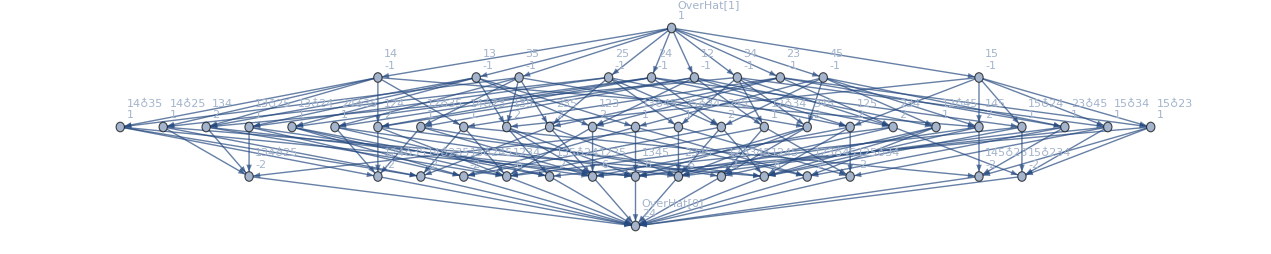

```mathematica
MobiusGraph5[K5Key,allGraphs5]
```

```mathematica
Incoming[part_]:=Sum[StirlingS2[Length[p],2],{p,part}]
```

```mathematica
ComputeFractionFormula[key_]:=Block[{vars=ListofVars[allGraphs5[key,"colofour"]],teller=Association[],noemer=Association[],colofour, deps=Association[],from1, to1},
Table[
colofour=allGraphs5[k,"colofour"];
teller[colofour]=0;
noemer[colofour]=0;
deps[colofour]={}
,
{k,allGraphs5AtomKeys}
];
Table[

from1=SetsToSymbol2[SymbolToSets[edge[[1]]]];
to1=SetsToSymbol2[SymbolToSets[edge[[2]]]];
AppendTo[deps[from1],to1];
noemer[to1]+=1;

,
{edge,EdgeList[MobiusGraph5[K5Key,allGraphs5]]}
];

Table[Table[teller[dep]+=1,{dep,deps[v]}],{v,vars}];

Sum[
With[{colofour2=allGraphs5[k,"colofour"]},

If[noemer[colofour2]==0,
Framed[colofour2],
teller[colofour2]/noemer[colofour2]*colofour2
]
]
,
{k,allGraphs5AtomKeys}
]
]
```

```mathematica
ComputeFractionFormula[starKey]/.RepGraph["C"]
```

-Graphics-295240+(-Graphics-582881)/7+(-Graphics-567701)/7+(-Graphics-560121)/2+(-Graphics-522321)/7+(-Graphics-499721)/2+(-Graphics-492201)/2+(-Graphics-390141)/7+(-Graphics-326841)/2+(-Graphics-305861)/2+(-Graphics-298881)/7+(2 -Graphics-560111)/3+(-Graphics-514750)/3+-Graphics-492161+(2 -Graphics-499631)/3+(-Graphics-492100)/2+-Graphics-492081+(-Graphics-382810)/3+(-Graphics-319540)/2+(2 -Graphics-298571)/3+(-Graphics-368170)/3+-Graphics-304961+(-Graphics-297970)/3+(-Graphics-360860)/2+-Graphics-297681+(2 -Graphics-324411)/3+(-Graphics-303340)/2+(-Graphics-296330)/3+-Graphics-302621+(-Graphics-295600)/2+(2 -Graphics-295371)/3+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270

```mathematica
ComputeFractionFormula[lambdaKey]/.RepGraph["C"]
```

-Graphics-295240+(-Graphics-582881)/7+(-Graphics-567701)/7+(-Graphics-522321)/7+(-Graphics-514780)/2+(-Graphics-390141)/7+(-Graphics-298881)/7+(-Graphics-319840)/2+(-Graphics-368980)/2+(-Graphics-361940)/2+(-Graphics-383080)/2+(-Graphics-560111)/3+(2 -Graphics-514750)/3+(-Graphics-499631)/3+(-Graphics-492100)/2+(2 -Graphics-382810)/3+(-Graphics-319540)/2+(-Graphics-298571)/3+-Graphics-361660+(2 -Graphics-368170)/3+(2 -Graphics-297970)/3+-Graphics-361120+(-Graphics-360860)/2+(-Graphics-324411)/3+(-Graphics-303340)/2+(2 -Graphics-296330)/3+-Graphics-317380+(-Graphics-295600)/2+(-Graphics-295371)/3+-Graphics-317140+-Graphics-296080+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270

```mathematica
ComputeFractionFormula[1]/.RepGraph["C"]
```

-Graphics-295240+(8 -Graphics-590481)/15+-Graphics-582881+-Graphics-567701+(-Graphics-560121)/4+(4 -Graphics-522321)/7+-Graphics-499721+(-Graphics-492201)/2+-Graphics-514780+(4 -Graphics-390141)/7+(-Graphics-326841)/2+-Graphics-305861+(4 -Graphics-298881)/7+-Graphics-319840+-Graphics-368980+(-Graphics-361940)/2+-Graphics-383080+-Graphics-560111+-Graphics-514750+-Graphics-492161+-Graphics-499631+-Graphics-492100+(-Graphics-492081)/2+-Graphics-382810+-Graphics-319540+-Graphics-298571+-Graphics-361660+-Graphics-368170+-Graphics-304961+-Graphics-297970+-Graphics-361120+(-Graphics-360860)/2+(-Graphics-297681)/2+(2 -Graphics-324411)/3+-Graphics-303340+(2 -Graphics-296330)/3+-Graphics-317380+-Graphics-302621+-Graphics-295600+(2 -Graphics-295371)/3+-Graphics-317140+-Graphics-296080+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270

```mathematica
allGraphs5[1,"colofournull"]
```

p1x2x3x45

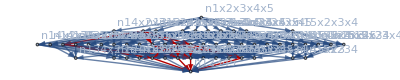

```mathematica
Graph[EdgeList[MobiusGraph5[K5Key,allGraphs5]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->"Name",
GraphHighlight->EdgeList[MobiusGraph5[alfaKey,allGraphs5]]]
```

First::nofirst: {} has zero length and no first element.

SymbolName::sym: Argument Missing[KeyAbsent,35977] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,35977]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Missing[KeyAbsent,35977]],1],x].

StringLength::string: String expected at position 1 in StringLength[StringDrop[SymbolName[Missing[KeyAbsent,35977]],1]].

StringSplit::argb: StringSplit called with 0 arguments; between 1 and 3 arguments are expected.

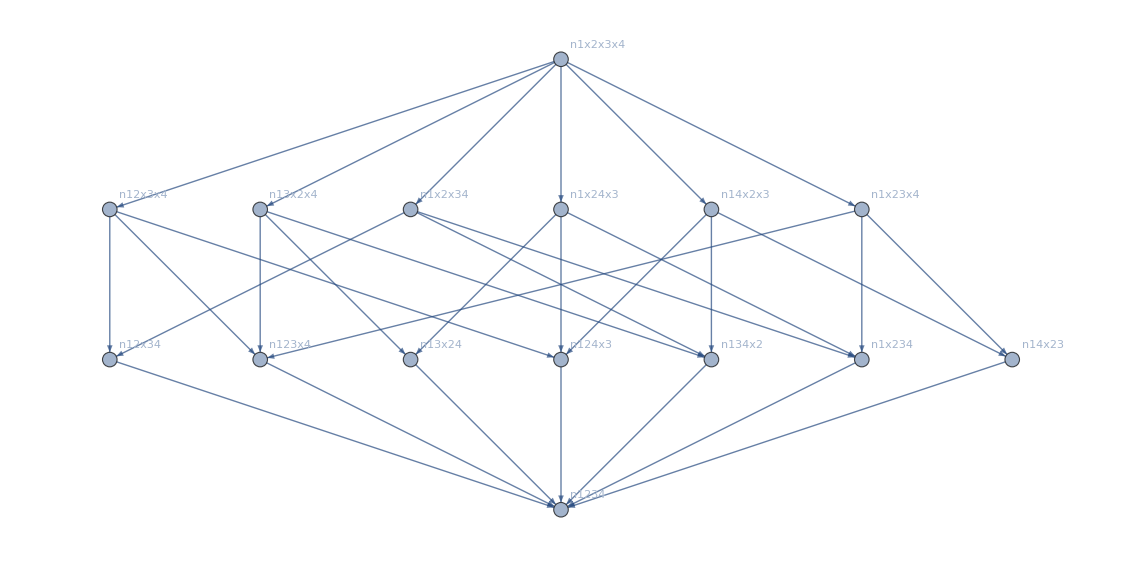

```mathematica
Graph[EdgeList[MobiusGraph5[K4Key,allGraphs4]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->"Name",
GraphHighlight->EdgeList[MobiusGraph5[alfaKey,allGraphs4]]]
```

```mathematica
ComputeFractionFormula4[key_]:=Block[{vars=ListofVars[allGraphs4[key,"colofour"]],teller=Association[],noemer=Association[],colofour, deps=Association[],from1, to1},
Table[
colofour=allGraphs4[k,"colofour"];
teller[colofour]=0;
noemer[colofour]=0;
deps[colofour]={}
,
{k,allGraphs4AtomKeys}
];
Table[
from1=SetsToSymbol2[SymbolToSets[edge[[1]]]];
to1=SetsToSymbol2[SymbolToSets[edge[[2]]]];
AppendTo[deps[from1],to1];
noemer[to1]+=1;
,
{edge,EdgeList[MobiusGraph5[K4Key,allGraphs4]]}
];

Table[Table[
(*Print[v, " has dependency ",dep];*)
teller[dep]+=1,
{dep,deps[v]}],
{v,vars}];

Sum[
With[{colofour2=allGraphs4[k,"colofour"]},

If[noemer[colofour2]==0,
Framed[colofour2],
teller[colofour2]/noemer[colofour2]*colofour2
]
]
,
{k,allGraphs4AtomKeys}
]
]
```

```mathematica
ComputeFractionFormula4[1]/.RepGraph4["C"]
```

(4 v1234)/7+v123x4+v124x3+v12x34/2+v12x3x4+(2 v134x2)/3+v13x24+v13x2x4+v14x23+v14x2x3+(2 v1x234)/3+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4

vars={v123x4,v124x3,v12x3x4,v13x24,v13x2x4,v14x23,v14x2x3,v1x23x4,v1x24x3,v1x2x3x4}

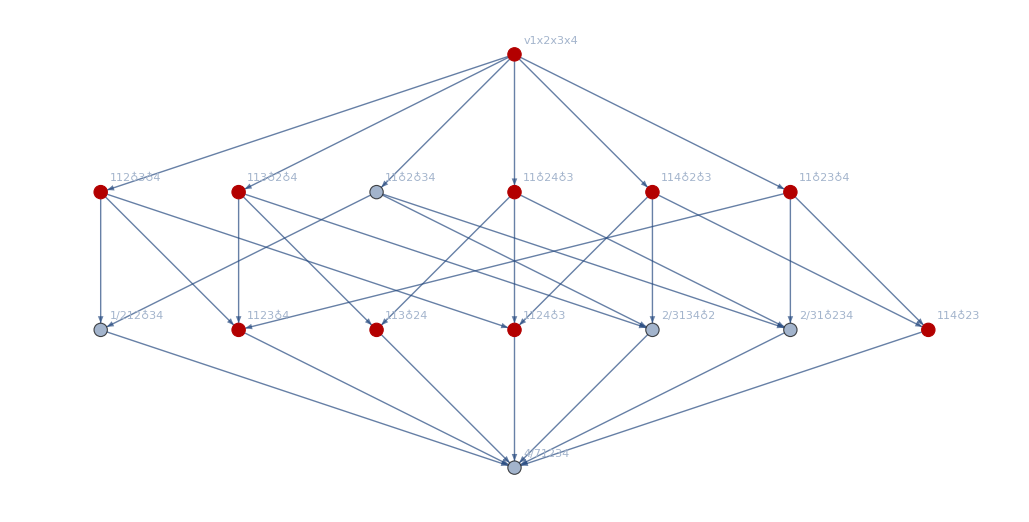

```mathematica
Graph[EdgeList[MobiusGraph5[K4Key,allGraphs4]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->With[{formula=ComputeFractionFormula4[1]},
Table[ChangeSymbol[allGraphs4[k,"colofour"],"n"]->

If[Coefficient[formula,allGraphs4[k,"colofour"]]≠0,
Row [{Style[Coefficient[formula,allGraphs4[k,"colofour"]],20,Red],SymbolToLabel[allGraphs4[k,"colofour"]]}]
,
allGraphs4[k,"colofour"]
]


,{k,allGraphs4AtomKeys}]],
GraphHighlight->Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs4[1,"colofour"]]]]
```

```mathematica
ShowFraction[key_]:=Graph[EdgeList[MobiusGraph5[K5Key,allGraphs5]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->With[{formula=ComputeFractionFormula[key]},
Table[ChangeSymbol[allGraphs5[k,"colofour"],"n"]->

If[Coefficient[formula,allGraphs5[k,"colofour"]]≠0,
Rotate[Row [{Framed[Style[Coefficient[formula,allGraphs5[k,"colofour"]],10,Red,Bold]],SymbolToLabel[allGraphs5[k,"colofour"]]}],Pi/4]
,
Style[allGraphs5[k,"colofour"],8]
]


,{k,allGraphs5AtomKeys}]],
GraphHighlight->Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs5[key,"colofour"]]],
ImageSize->800,
AspectRatio->1]
```

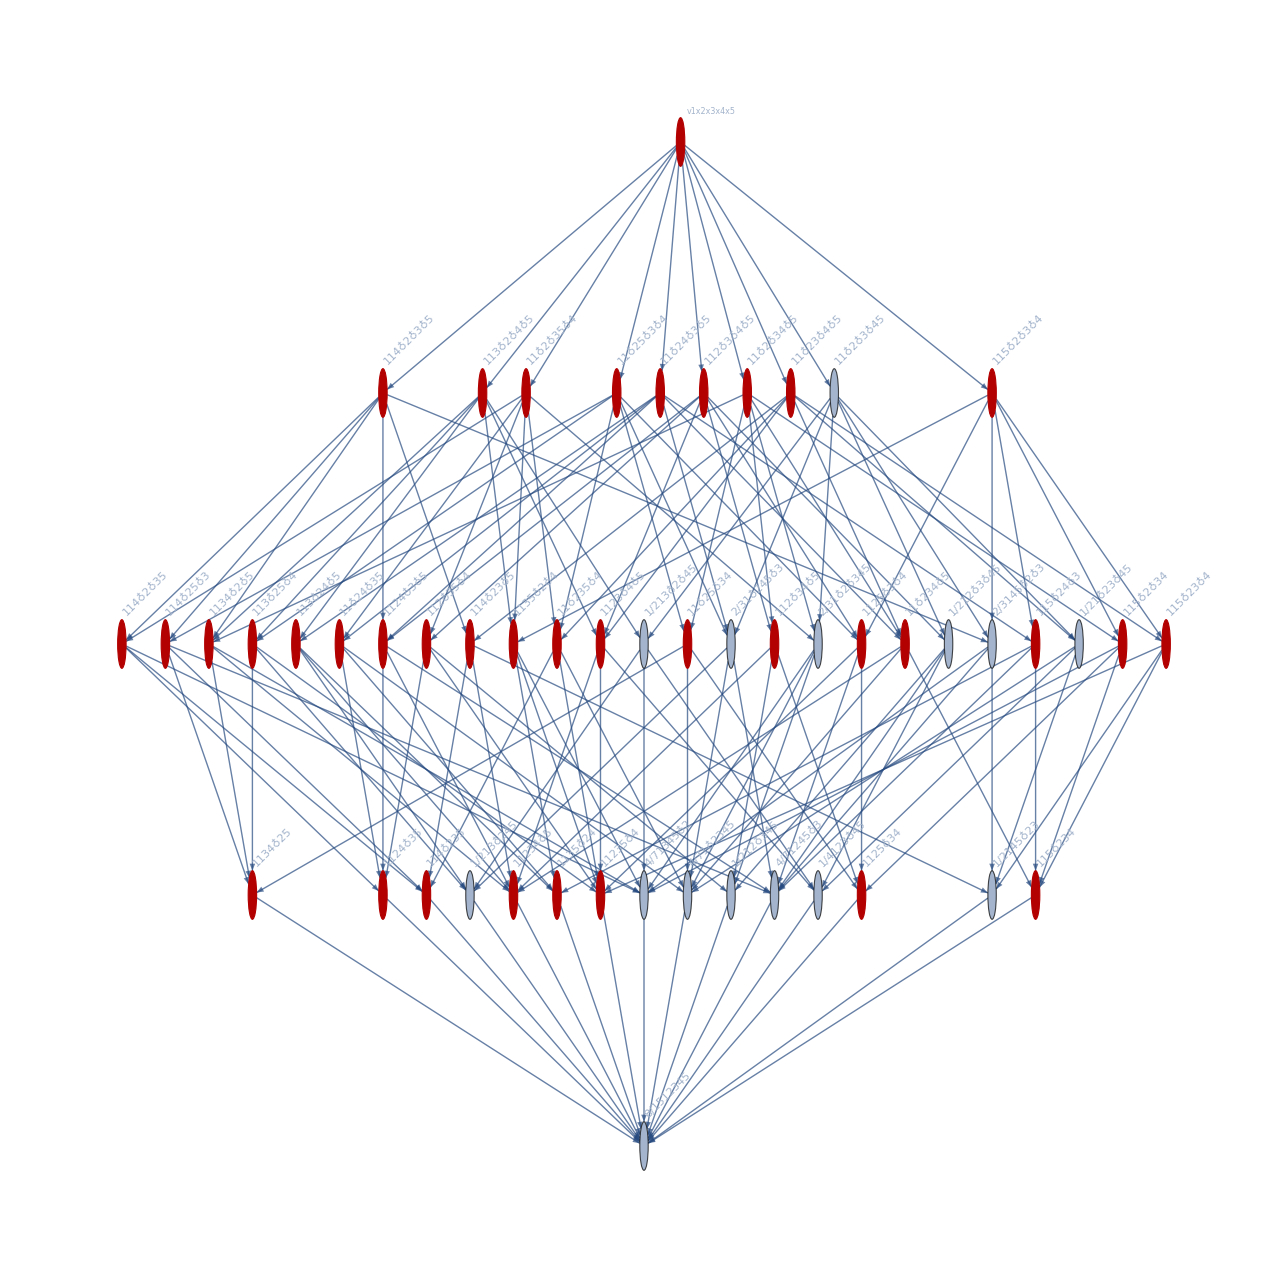

```mathematica
ShowFraction[1]
```